# Part A Define functions for plotting images of data

-Graphics-

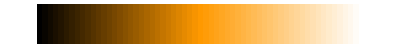

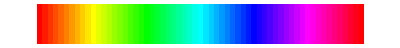

```mathematica
PlotTable[table_,z_,cf_,m_,M_,a_,label_]:=Module[{sizex,sizey},
sizey=Length[table];
sizex=Length[table[[1]]];
Show[ArrayPlot[Reverse[table],ImageSize->Round[z*sizex],PlotRangePadding->0,ColorFunctionScaling->False,ColorFunction->cf[m,M,a],PlotLabel->label<>", Size: "<>ToString[{sizex,sizey}],DataRange->{{1,sizex},{1,sizey}}]]
];
PlotTableConstrained[table_,cf_,m_,M_,a_]:=Module[{sizex,sizey},
sizey=Length[table];
sizex=Length[table[[1]]];
ArrayPlot[Reverse[table],ImageSize->sizex,PixelConstrained->True, PlotRangePadding->0,ColorFunctionScaling->False,ColorFunction->cf[m,M,a],DataRange->{{1,sizex},{1,sizey}}]
];
ColFuncSpot[m_,M_,a_]:=Function[If[#!=0,Green,Opacity[0,White]]];
ColFuncMapDIS[m_,M_,a_]:=Function[Blend[{Black,White},((#-m)/(M-m))^a]];
ColFuncMapPHASE[m_,M_,a_]:=Function[Hue[((#-m)/(M-m))^a]];
ColFuncMapCDW[m_,M_,a_]:=Function[Blend[{Black,Hue[0.1],White},((#-m)/(M-m))^a]];
ArrayPlot[{Table[ x,{x,0,1,1/60}]},ColorFunctionScaling->False,AspectRatio->0.1,ColorFunction->ColFuncMapDIS[0,1,1]]
ArrayPlot[{Table[ x,{x,0,1,1/60}]},ColorFunctionScaling->False,AspectRatio->0.1,ColorFunction->ColFuncMapCDW[0,1,1]]
ArrayPlot[{Table[ x,{x,0,1,1/60}]},ColorFunctionScaling->False,AspectRatio->0.1,ColorFunction->ColFuncMapPHASE[0,1,1]]
```

# Part B Set parameters of training set: smooth disorder strengths and lengthscales, dislocation number, image size (see the comments)

```mathematica
(*Subscript[ϕ, 0] the initial phase of CDW*)
fi0=π/4;
(*Prefactor of sFF component in CDW; the dFF has prefactor =1*)
cS=0.5;


(*Smooth disorder intensities Subscript[ϵ, A] and Subscript[ϵ, ϕ]*)
epsA=0.8;
epsT=0.5;
(*Smooth disorder correlation lengthscales Subscript[ξ, A] and Subscript[ξ, ϕ]*)
(*NB: In published paper, both equal 8*)
flA=8;
flf=6;

(*Number of dislocations*)
ndd=2;
(*A sublist is chosen randomly to assign windings to the dislocations: "1"=+2π, "2"=-2π*)
dislsgn={{1,2},{2,1}};
(*Amplitude field of dislocation recovers with this characteristic lengthscale (in units of pixels)*)
dislwidth=2.;

(*Choosing Q values*)
(*List of category labels assigned to images. Category label appears at the end of each imagedata.*)
qqind={1,2,3,4};
(*Corresponding list of Q values, in units of 2π/a*)
qqval={0.23,0.25,0.27,0.29};

(*In final image the square lattice is along the diagonal, with total number of CuO2 unit-cells equal to 2*X*Y*)
(*In published paper the X=Y=86*)
X=43;
Y=43;
(*Number of pixels in Cu-Cu distance (along diagonal in image)*)
pixperUC=6;
(*Resulting image size*)
pixX=X*pixperUC;
pixY=Y*pixperUC;
pixsize=pixX;
```

# Part C Functions for creating&convoluting fields on a 2D pixelated image. Used for creating atomic lattice with given FF, amp&phase field of single dislocation, and smooth disorder fields.

## - “AtomGaussMask” function: creates 2d image of format “pixx”X”pixy” where at each site (sites are pixel coordinates input by list “apos”) one adds or subtracts (determined by input list “sgns”) a 2D Gaussian of width=“width” in pixels. “Smooth2D” function: filters a Fourier transform of 2d image (input “ft”, periodic boundary conditions implemented), by multiplying it with a mask (square image of dimensions l_1Xl_2 with pixel values “vals” and zero outside the square). “valsf” and “valsA” lists: specific filters used to create random phase and random amplitude fluctuation fields. Each filter is a 2d Gaussian. Their widths are inversely proportional to desired correlation lengthscales, i.e., the lengthscale parameters “flf” and “flA”, because they are FTs of the real-space 2d Gaussians. “dislfields” function: returns (1) a 2d image “dislccwA”, the amplitude field of single dislocation at origin with exponential recovery lengthscale “w” (input) in pixels; and (2) two 2d images “dislc(c)wF” of the dislocation’s phase with winding +/-2π.

```mathematica
AtomGaussMask[{pixx_,pixy_},apos_,sgns_,width_]:=Module[{i,j,a,at,b,c,mask,pp,l1,l2,vals},
mask=Table[0,{pixy},{pixx}];
l1=Round[-4width];
l2=Round[4width];
vals={};
For[b=l1,b≤l2,b++,
For[c=l1,c≤l2,c++,
AppendTo[vals,Exp[-(b^2+c^2)/(2. width^2)]];
];
];
For[a=1,a≤Length[apos],a++,
If[sgns[[a]]≠0,
at=apos[[a]];
For[b=l1,b≤l2,b++,
For[c=l1,c≤l2,c++,
If[(at[[1]]+b>0)&&(at[[1]]+b≤pixx)&&(at[[2]]+c>0)&&(at[[2]]+c≤pixy),
pp=at+{b,c};
mask[[pp[[2]],pp[[1]]]]+=sgns[[a]]*vals[[(b-l1)*(l2-l1+1)+(c-l1)+1]];
];
];
];
];
];
mask=mask/Max[Abs[mask]];
Return[mask];
];

Smooth2d[ft_,l1_,l2_,vals_]:=Module[{b,c,x,y,lenx,leny,lis},
leny=Length[ft];
lenx=Length[ft[[1]]];
lis=Table[0,{leny},{lenx}];
For[b=l1,b≤l2,b++,
If[b<0,x=lenx+1+b,x=1+b];
For[c=l1,c≤l2,c++,
If[c<0,y=leny+1+c,y=1+c];
lis[[y,x]]=ft[[y,x]]*vals[[(b-l1)*(l2-l1+1)+(c-l1)+1]];
];
];
Return[lis];
];

(*Create valsf and valsA data*)
valsf={};
valsA={};
points=pixX;
lam=points/(π*flA*pixperUC);
lfi=points/(π*flf*pixperUC);
l1f=Round[-4lfi];
l2f=Round[4lfi];
If[l2f>points,Print["Too small flf!"]];
For[b=l1f,b≤l2f,b++,
For[c=l1f,c≤l2f,c++,
AppendTo[valsf,Exp[-(b^2+c^2)/(2. lfi^2)]];
];
];
l1A=Round[-4lam];
l2A=Round[4lam];
If[l2A>points,Print["Too small flA!"]];
For[b=l1A,b≤l2A,b++,
For[c=l1A,c≤l2A,c++,
AppendTo[valsA,Exp[-(b^2+c^2)/(2. lam^2)]];
];
];

dislfields[pix_,w_]:=Module[{siz,dislccwA,dislccwF,dislcwF,cx,cy,x,y},
siz=2pix+1;
dislccwA=Table[0,{siz},{siz}];
dislccwF=Table[0,{siz},{siz}];
cx=1;
cy=1;
For[x=-pix,x≤pix,x++,
For[y=-pix,y≤pix,y++,
dislccwA[[cx,cy]]=(1.-Exp[-(√(x^2+y^2))/(1.w)]);
dislccwF[[cx,cy]]=If[x==0&&y==0,0,Mod[1.Arg[x+I y],2π]];
cy++;
];
cy=1;
cx++;
];
dislcwF=Reverse[dislccwF];
dislccwA=RotateLeft[RotateLeft[#,pix]&/@dislccwA,pix];
dislccwF=RotateLeft[RotateLeft[#,pix]&/@dislccwF,pix];
dislcwF=RotateLeft[RotateLeft[#,pix]&/@dislcwF,pix];
Return[{dislccwA,{dislccwF,dislcwF}}];
];
```

# Part D Create and plot atomic lattices with sFF and dFF

```mathematica
(*"blob" parameters determine width (in units of Cu-Cu pixel distance) of Gaussians which are put onto lattice sites.
Values are chosen to visually correspond to experiments.*)
blobw=0.35*pixperUC;
Sblobw=0.35*pixperUC;
Kblobw=0.2*pixperUC;

shft=Round[pixperUC/4];
(*atom coordinates on CuO2 plane; "oo" is position at center of plaquette*)
cu=Flatten[Table[pixperUC*{x,y}+{1,1}+{shft,shft},{x,-1,X+1},{y,-1,Y+1}],1];
ox=Flatten[Table[pixperUC*{x+1/2,y}+{1,1}+{shft,shft},{x,-1,X+1},{y,-1,Y+1}],1];
oy=Flatten[Table[pixperUC*{x,y+1/2}+{1,1}+{shft,shft},{x,-1,X+1},{y,-1,Y+1}],1];
oo=Flatten[Table[pixperUC*{x+1/2,y+1/2}+{1,1}+{shft,shft},{x,-1,X+1},{y,-1,Y+1}],1];
atoms=Join[cu,ox,oy,oo];

(*signs that have to be given to Gaussian blobs to get an intra-unit-cell FF*)
(*There are 4 FF's: D,S, Splus, and finally "Ko" is an auxilliary FF which has weight at center of plaquette where there are no atoms*)
sigD=Join[Table[0,{Length[cu]}],Table[1,{Length[ox]}],Table[-1,{Length[oy]}],Table[0,{Length[oo]}]];
sigS=Join[Table[1,{Length[cu]}],Table[0,{Length[ox]}],Table[0,{Length[oy]}],Table[0,{Length[oo]}]];
sigSp=Join[Table[0,{Length[cu]}],Table[1,{Length[ox]}],Table[1,{Length[oy]}],Table[0,{Length[oo]}]];
sigKo=Join[Table[0,{Length[cu]}],Table[0,{Length[ox]}],Table[0,{Length[oy]}],Table[-1,{Length[oo]}]];

(*The FF atomic lattices are created here*)
mD=AtomGaussMask[{pixX,pixY},atoms,sigD,blobw];
mS=AtomGaussMask[{pixX,pixY},atoms,sigS,Sblobw];
mKo=AtomGaussMask[{pixX,pixY},atoms,sigKo,Kblobw];
mKo=(mKo-Max[mKo])/(Max[mKo]-Min[mKo]);
```

## Plot FF atomic lattices: dFF vs. sFF

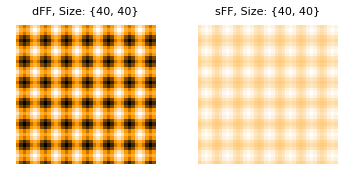

```mathematica
(*NOTES:
dFF (left image) has opposite peaks (white) and dips (black) at Ox and Oy atom positions.
sFF (right image) has peaks only at Cu positions, the rest is equally flat.*)
(*Only a portion is plotted from entire 258x258 pixel images.*)
(*X and Y axes are horizontal/vertical*)
portionsize=40;
mDportion=#[[1;;portionsize]]&/@mD[[1;;portionsize]];
mSportion=#[[1;;portionsize]]&/@mS[[1;;portionsize]];
GraphicsGrid[{{
PlotTable[mDportion,4,ColFuncMapCDW,-1,1,1,"dFF"],
PlotTable[mSportion,4,ColFuncMapCDW,-1,1,1,"sFF"]}}]
```

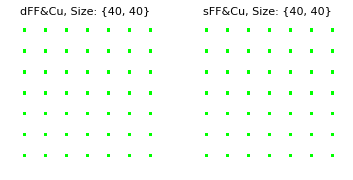

```mathematica
(*Green dots are Cu coordinates*)
cumark=Table[0,{y,1,portionsize},{x,1,portionsize}];
For[m=1,m≤Length[cu],m++,If[cu[[m,1]]>0&&cu[[m,1]]<=portionsize&&cu[[m,2]]>0&&cu[[m,2]]<=portionsize,cumark[[cu[[m,1]],cu[[m,2]]]]=1]];
GraphicsGrid[{{
Show[PlotTable[mDportion,4,ColFuncMapCDW,-1,1,1,"dFF&Cu"],PlotTable[cumark,1,ColFuncSpot,0,1,1,"Cu"]],
Show[PlotTable[mSportion,4,ColFuncMapCDW,-1,1,1,"sFF&Cu"],PlotTable[cumark,1,ColFuncSpot,0,1,1,"Cu"]]}}]
```

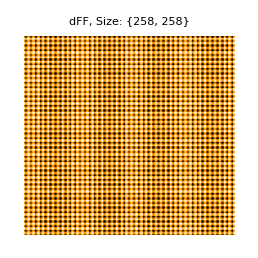

```mathematica
(*Entire image of dFF atomic lattice*)
PlotTable[mD,1,ColFuncMapCDW,-1,1,1,"dFF"]
```

# Part E Generate random fluctuation fields and random dislocation fields.

## E1) Create smooth fluctuation field (it gives the general recipe), used for dFF amplitude

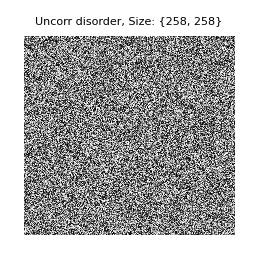

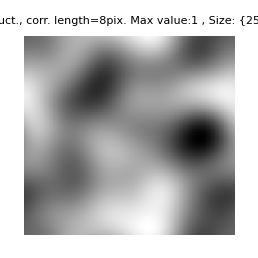

```mathematica
(*FIRST, we take uncorrelated pixel values*)
amdis=Table[RandomReal[{-1,1}],{y,1,pixX},{x,1,points}];
(*PLOT image*)
PlotTable[amdis,1,ColFuncMapDIS,Min[amdis],Max[amdis],1,"Uncorr disorder"]
(*SECOND, convolute this image with Gaussian of width given by chosen (Part B) correlation length of amplitude fluctuations "flA".
The convolution is achieved by multiplying Fourier transforms, done by function "Smooth2d".
*)
(*"valsA" list contains numerical values of FT of our 2d Gaussian.*)
ftamdis=Fourier[amdis];
sftamdis=Smooth2d[ftamdis,l1A,l2A,valsA];
(*THIRD, Inverse Fourier to complete convolution, and normalize fluctuations between -1 and 1.*)
samdis=Chop[InverseFourier[sftamdis]/Max[Abs[InverseFourier[sftamdis]]]];
(*PLOT image*)
PlotTable[samdis,1,ColFuncMapDIS,Min[samdis],Max[samdis],1,"Ampl. fluct., corr. length="<>ToString[flA]<>"pix"<>". Max value:1\n"]
```

```mathematica
{ddA,ddF}=dislfields[pixX,dislwidth];
```

## E2) Create smooth fluctuation field for dFF phase; same as for amplitude, except use different correlation length (“flf” from Part B), and normalize fluctuations from -π to π.

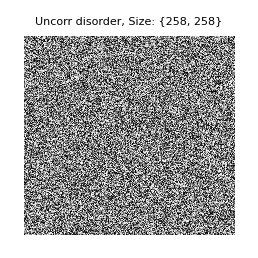

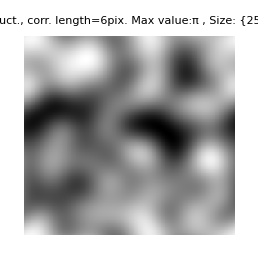

```mathematica
fidis=Table[RandomReal[{-1,1}],{y,1,pixX},{x,1,points}];
(*PLOT image*)
PlotTable[fidis,1,ColFuncMapDIS,Min[fidis],Max[fidis],1,"Uncorr disorder"]
ftfidis=Fourier[fidis];
sftfidis=Smooth2d[ftfidis,l1f,l2f,valsf];
sfidis=π*Chop[InverseFourier[sftfidis]/Max[Abs[InverseFourier[sftfidis]]]];
(*PLOT image*)
PlotTable[sfidis,1,ColFuncMapDIS,Min[sfidis],Max[sfidis],1,"Phase fluct., corr. length="<>ToString[flf]<>"pix"<>". Max value:π\n"]
```

## E3) Create smooth fluctuation amplitude and phase fields for sFF component; same parameters as for dFF, but a different random realization.

```mathematica
Sfidis=Table[RandomReal[{-1,1}],{y,1,pixX},{x,1,points}];
Sftfidis=Fourier[Sfidis];
Ssftfidis=Smooth2d[Sftfidis,l1f,l2f,valsf];
Ssfidis=π Chop[InverseFourier[Ssftfidis]/Max[Abs[InverseFourier[Ssftfidis]]]];
Samdis=Table[RandomReal[{-1,1}],{y,1,pixX},{x,1,points}];
Sftamdis=Fourier[Samdis];
Ssftamdis=Smooth2d[Sftamdis,l1A,l2A,valsA];
Ssamdis=Chop[InverseFourier[Ssftamdis]/Max[Abs[InverseFourier[Ssftamdis]]]];
```

## E4) Create field due to randomly positioned dislocations (used only for dFF).

```mathematica
(*FIRST, Amplitude and phase fields of single dislocation in corner (periodic boundaries), given amplitude recovery length (Part B)*)
(*These images are twice the size of our lattice, because even if the dislocation is in a corner of our lattice, its field needs to cover the entire lattice*)
{ddA,ddF}=dislfields[pixX,dislwidth];
```

```mathematica
(*PLOT, with dislocation shifted to center*)
Print["Dislo ampl. field, recovery length="<>ToString[dislwidth]<>"pix"<>".\n Max value:"<>ToString[Max[ddA]]]
PlotTableConstrained[RotateRight[#,pixX]&/@RotateRight[ddA,pixX],ColFuncMapDIS,Min[ddA],Max[ddA],1]
Print["Dislo phase field, winding +2π"<>"\n Max value:"<>ToString[Max[ddF[[1]]]]]
PlotTableConstrained[RotateRight[#,pixX]&/@RotateRight[ddF[[1]],pixX],ColFuncMapPHASE,Min[ddF[[1]]],Max[ddF[[1]]],1]
Print["Dislo phase field, winding -2π"<>"\n Max value:"<>ToString[Max[ddF[[1]]]]]
PlotTableConstrained[RotateRight[#,pixX]&/@RotateRight[ddF[[2]],pixX],ColFuncMapPHASE,Min[ddF[[2]]],Max[ddF[[2]]],1]
```

Dislo ampl. field, recovery length=2.pix.
 Max value:1.

-Graphics-

Dislo phase field, winding +2π
 Max value:6.27931

-Graphics-

Dislo phase field, winding -2π
 Max value:6.27931

-Graphics-

```mathematica
(*SECOND, Pick random coordinates for each dislo, but keep them in the central diamond of the square which corresponds to our lattice, because this diamond will become the final image after rotation by 45 degrees to match exp image orientation.*)
ddpos=Table[0,{ndd}];
For[dp=1,dp≤ndd,dp++,dpc={RandomInteger[{1,pixX/2}],RandomInteger[{1,pixY/2}]};
dpc={dpc[[2]]+dpc[[1]],dpc[[2]]-dpc[[1]]}+{0,pixY/2};
ddpos[[dp]]=Round[dpc];
];
ddsgn=dislsgn[[RandomInteger[{1,Length[dislsgn]}]]];
(*THIRD, multiply amplitude fields centered on random positions of dislocations, while adding the phase fields*)
ddAfield=Product[RotateRight[RotateRight[#,ddpos[[i,2]]]&/@ddA,ddpos[[i,1]]],{i,1,ndd}];
ddFfield=Sum[RotateRight[RotateRight[#,ddpos[[i,2]]]&/@ddF[[ddsgn[[i]]]],ddpos[[i,1]]],{i,1,ndd}];
(*We can now cut out the square corresponding to our latice image. The dislocations should be located inside the central diamond of this image.*)
ddAfield=#[[1;;pixX]]&/@ddAfield[[1;;pixX]];
ddFfield=#[[1;;pixX]]&/@ddFfield[[1;;pixX]];
```

Dislo ampl. field total, recovery length=2.pix.
 Max value:1.

-Graphics-

Dislo phase field total
 Max value:6.27931

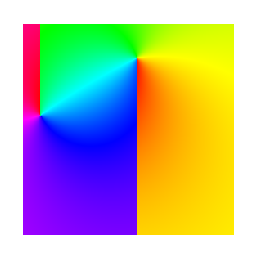

```mathematica
(*PLOT total dislocation amplitude and phase contributions*)
Print["Dislo ampl. field total, recovery length="<>ToString[dislwidth]<>"pix"<>".\n Max value:"<>ToString[Max[ddA]]]
PlotTableConstrained[ddAfield,ColFuncMapDIS,Min[ddAfield],Max[ddAfield],1]
Print["Dislo phase field total"<>"\n Max value:"<>ToString[Max[ddF[[1]]]]]
PlotTableConstrained[ddFfield,ColFuncMapPHASE,Min[ddFfield],Max[ddFfield],1]
```

# Part F Procedure for a chosen Q: 1) Use the fields from E to generate the sFF and dFF field components of CDW (see Methods equations for I_c). Multiply the sFF and dFF fields with atomic lattice images. 2) Rotate the image so x-axis is along diagonal, normalize image. (Optionally, write to output file). Finally, 3) The results are shown for all Q’s. BEYOND this DEMO: repeat all in loop, creating images for many instances of random fields.

## F1) Combine all fields, and apply to atomic lattice. Demonstrate procedure for one Q, then show results for all Q’s in F3.

```mathematica
(*Choose the first category*)
qq=1;
(*NOTE: its category label is qqind[[1]]*)
(*Q is numerical value of wavevector in units of 2π*)
Q=qqval[[qq]];

(*wq is the intensity field Subscript[I, c] (see Methods) for this Q and belonging to dFF.
It combines CDW Q with smooth and dislocaiton fields.*)
wq=Table[(1+epsA*samdis[[y,x]])*ddAfield[[y,x]]*Cos[2*π*Q*(x-shft-1)/pixperUC+fi0+epsT*sfidis[[y,x]]+ddFfield[[y,x]]],{y,1,pixY},{x,1,pixX}];
(*PLOT*)
Print["Intensity field for dFF: smooth ampl&phase fluctutations and dislocations. The Q is "<>ToString[Q]]
PlotTableConstrained[wq,ColFuncMapDIS,Min[wq],Max[wq],1]
```

Intensity field for dFF: smooth ampl&phase fluctutations and dislocations. The Q is 0.23

-Graphics-

Final dFF component: Intensity field multiplied by atomic lattice for dFF. The Q is 0.23

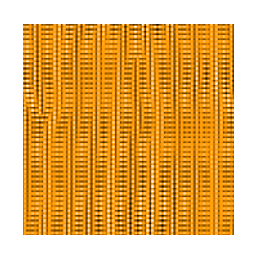

```mathematica
(*cdmd is complete image of dFF component.*)
(*Multiply intensity field with atomic lattice of dFF; The second line reduces the signal in plaquette centers where there are no atoms.*)
cdmd=mD*wq;
cdmd+=0.6*Abs[Min[cdmd]]*mKo;
(*PLOT*)
Print["Final dFF component: Intensity field multiplied by atomic lattice for dFF. The Q is "<>ToString[Q]]
PlotTableConstrained[cdmd,ColFuncMapCDW,Min[cdmd],Max[cdmd],1]
```

Intensity field for sFF: smooth ampl&phase fluctutations only; NO wave with Q and NO dislocations

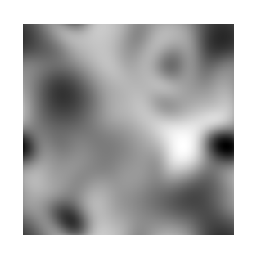

```mathematica
(*wqS is the intensity field Subscript[I, c] (see Methods) belonging to sFF component.
It does not depend on Q, and has no dislocations.*)
wqS=Table[(1+epsA*Ssamdis[[y,x]])*Cos[epsT*Ssfidis[[y,x]]],{y,1,pixY},{x,1,pixX}];
(*PLOT*)
Print["Intensity field for sFF: smooth ampl&phase fluctutations only; NO wave with Q and NO dislocations"]
PlotTableConstrained[wqS,ColFuncMapDIS,Min[wqS],Max[wqS],1]
```

Final sFF component: Intensity field multiplied by atomic lattice for sFF.

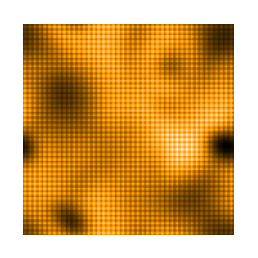

```mathematica
(*cdms is complete image of sFF component.*)
(*NOTE: The sFF is localized on Cu sites, not the oxygens.*)
cdms=cS*mS*wqS;
(*PLOT*)
Print["Final sFF component: Intensity field multiplied by atomic lattice for sFF."]
PlotTableConstrained[cdms,ColFuncMapCDW,Min[cdms],Max[cdms],1]
```

Final image is sum of sFF and dFF components.

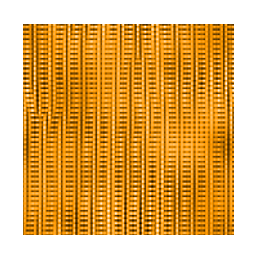

```mathematica
(*Final image is sum of dFF and sFF components*)
cdm=cdmd+cdms;
(*PLOT*)
Print["Final image is sum of sFF and dFF components."]
PlotTableConstrained[cdm,ColFuncMapCDW,Min[cdm],Max[cdm],1]
```

## F2) To match experimental images, rotate the image (variable cdm) by 45 degrees.

Rotated by 45 degrees, and rescaled area by 2.

-Graphics-

Cut out central square.

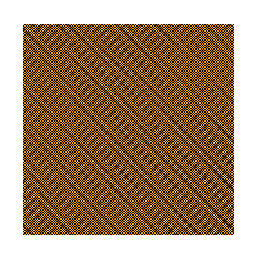

```mathematica
(*We preserve each individual (square-shaped) pixel, both its size and orientation.
Hence our transformation only moves a pixel to the position determined by rotation. To prevent the pixels from overlapping, the rotating movement is accompanied by a √2 scaling.
The pixels in new positions hence form a diamond-shaped image of twice the area than original image, and fit into a square (variable "tt") of twice the side than the original ("cdm").
Yet each pixel has four nearest neighbor pixels which are empty (like a checkerboard pattern).
The empty pixels are assigned non-physical value -100.
*)
tt=Table[-100,{pixX*2},{pixY*2}];
For[it=1,it≤pixX,it++,
For[jt=1,jt≤pixX,jt++,
tt[[(it+jt-2)+1,(-it+jt-1+pixX)+1]]=cdmd[[it,jt]];
];
];
(*PLOT*)
Print["Rotated by 45 degrees, and rescaled area by 2."]
PlotTableConstrained[tt,ColFuncMapCDW,-2,Max[tt],1]
tt=tt[[pixX/2;;3 pixX/2-1,pixY/2;;3 pixY/2-1]];
(*PLOT*)
Print["Cut out central square."]
PlotTableConstrained[tt,ColFuncMapCDW,-2,Max[tt],1]
```

Final training image.

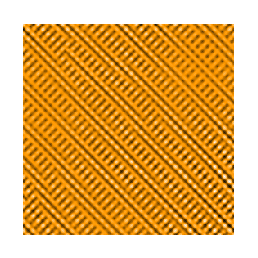

```mathematica
(*In "tt" the empty pixels are filled by interpolation from nearest neighbors (variable "nn").*)
(*The resulting image "tti" is normalized and ready to join the training set.*)
nn={{1,0},{0,1},{-1,0},{0,-1}};
tti=tt;
For[it=1,it≤pixX,it++,
For[jt=1,jt≤pixX,jt++,
If[tt[[it,jt]]==-100,
nnc=Select[({it,jt}+#)&/@nn,(#[[1]]>0&&#[[1]]≤pixX&&#[[2]]>0&&#[[2]]≤pixX)&];
tti[[it,jt]]=Mean[Table[tt[[nnc[[k,1]],nnc[[k,2]]]],{k,1,Length[nnc]}]];
];
];
];
tti=(tti-Min[tti])/(Max[tti]-Min[tti]);
(*PLOT*)
Print["Final training image."]
PlotTableConstrained[tti,ColFuncMapCDW,Min[tti],Max[tti],1]
```

How to output into file for ANN:
An example block of code is below, commented out.
All the training set images are written sequentially as a single list of numbers into a file read in by ANN.
 Each imagedata in the list is finished by an integer which labels the category of the image (from list “qqind”).

```mathematica
(*
(*Open output file*)
Clear[stf];
stf=OpenWrite["/Users/eunahkim/TrainingSetDEMO_2disl.csv"];
(*Write imagedata from variable "tti", and follow it by the category label; this should be done for each Q, i.e., make a loop hrough "qqind", and can be in an outer loop creating many realizations of random fields*)
WriteString[stf,({AccountingForm[#,8],","}&/@Chop[Flatten[tti]])/.List->Sequence];
Write[stf,qqind[[qq]]];
(*When the desired batch of images is made, close the output file*)
Close[stf];
*)
```

## F3) Demonstrate output for all Q’s. We just need to repeat procedure from F1 and F2, since the random fields (from part E)are fixed.

The values of Q/2π, in order, for each imagelist below are: 
{0.23, 0.25, 0.27, 0.29}

Intensity field for dFF: smooth ampl&phase fluctutations and dislocations.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Final dFF component: Intensity field multiplied by atomic lattice for dFF.

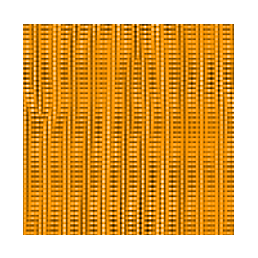
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Final image is sum of sFF and dFF components.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Final rotated training image.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Store produced images in these lists*)
wqlist={};
cdmdlist={};
cdmlist={};
ttilist={};

(*Cycle through categories*)
For[qq=1,qq≤Length[qqind],qq++,
(*Q is numerical value of wavevector in units of 2π*)
Q=qqval[[qq]];

(*wq is the intensity field Subscript[I, c] (see Methods) for this Q and belonging to dFF.
It combines CDW Q with smooth and dislocaiton fields.*)
wq=Table[(1+epsA*samdis[[y,x]])*ddAfield[[y,x]]*Cos[2*π*Q*(x-shft-1)/pixperUC+fi0+epsT*sfidis[[y,x]]+ddFfield[[y,x]]],{y,1,pixY},{x,1,pixX}];
AppendTo[wqlist,PlotTableConstrained[wq,ColFuncMapDIS,Min[wq],Max[wq],1]];
(*cdmd is complete image of dFF component.*)
(*Multiply intensity field with atomic lattice of dFF; The second line reduces the signal in plaquette centers where there are no atoms.*)
cdmd=mD*wq;
cdmd+=0.6*Abs[Min[cdmd]]*mKo;
AppendTo[cdmdlist,PlotTableConstrained[cdmd,ColFuncMapCDW,Min[cdmd],Max[cdmd],1]];
(*wqS is the intensity field Subscript[I, c] (see Methods) belonging to sFF component.
It does not depend on Q, and has no dislocations.*)
wqS=Table[(1+epsA*Ssamdis[[y,x]])*Cos[epsT*Ssfidis[[y,x]]],{y,1,pixY},{x,1,pixX}];
(*cdms is complete image of sFF component.*)
(*NOTE: The sFF is localized on Cu sites, not the oxygens.*)
cdms=cS*mS*wqS;
(*Final image is sum of dFF and sFF components*)
cdm=cdmd+cdms;
AppendTo[cdmlist,PlotTableConstrained[cdm,ColFuncMapCDW,Min[cdm],Max[cdm],1]];
tt=Table[-100,{pixX*2},{pixY*2}];
For[it=1,it≤pixX,it++,
For[jt=1,jt≤pixX,jt++,
tt[[(it+jt-2)+1,(-it+jt-1+pixX)+1]]=cdmd[[it,jt]];
];
];
tt=tt[[pixX/2;;3 pixX/2-1,pixY/2;;3 pixY/2-1]];
(*In "tt" the empty pixels are filled by interpolation from nearest neighbors (variable "nn").*)
(*The resulting image "tti" is normalized and ready to join the training set.*)
nn={{1,0},{0,1},{-1,0},{0,-1}};
tti=tt;
For[it=1,it≤pixX,it++,
For[jt=1,jt≤pixX,jt++,
If[tt[[it,jt]]==-100,
nnc=Select[({it,jt}+#)&/@nn,(#[[1]]>0&&#[[1]]≤pixX&&#[[2]]>0&&#[[2]]≤pixX)&];
tti[[it,jt]]=Mean[Table[tt[[nnc[[k,1]],nnc[[k,2]]]],{k,1,Length[nnc]}]];
];
];
];
tti=(tti-Min[tti])/(Max[tti]-Min[tti]);
AppendTo[ttilist,PlotTableConstrained[tti,ColFuncMapCDW,Min[tti],Max[tti],1]];
];
Print["\n\n The values of Q/2π, in order, for each imagelist below are: \n"<>ToString[qqval]<>"\n"];
Print["Intensity field for dFF: smooth ampl&phase fluctutations and dislocations."];
wqlist
Print["Final dFF component: Intensity field multiplied by atomic lattice for dFF."];
cdmdlist
Print["Final image is sum of sFF and dFF components."];
cdmlist
Print["Final rotated training image."];
ttilist
```